### Categorization

Tutorial

QNMSpectral

QNMSpectral`

QNMspectral/tutorial/SimpleExample

### Keywords

Details

# A simple example: a massless scalar in AdS_5

A technically simple example of a quasinormal mode that can only be computed numerically is that of a massless scalar field in an AdS_5 background.

We will illustrate the workings of this package by computing these modes.

This loads the package:

```mathematica
Needs["QNMspectral`"]
```

## The quasinormal mode equation

The action of a massless scalar field is given S = -1/2∫d^5 x ∂_μ ϕ∂^μ ϕ.

The method used for the numerical computation requires that the equation is written in Eddington-Finkelstein coordinates. The reason is that in these coordinates the condition that the perturbation be infalling at the horizon becomes merely the condition that the perturbation be regular at the horizon.

This allows us to impose the boundary condition there only implicitly, through expressing the perturbation as a sum of finite functions. For more on this see the section technical details below.

So we take the metric to be (we set the horizon at r=1, this is the default assumed value, but can be changed by setting Horizon)

ds^2= - f(r) dt^2+2 dt dr + r^2 dx^2, with f(r) = r^2(1-r^-4).

In these coordinates the boundary is at r→∞. This is ofcourse inconvenient for the numerics, so we first transform to u=1/r, to get

ds^2= - f(u) dt^2-2/u^2 dt du + u^-2 dx^2, with f(u) = u^-2(1-u^4).

Now we take a quasinormal mode ansatz for ϕ:

ϕ(u,t,y) = 0 + δϕ(u,t,y) = δϕ(u) e^(-i(ω t - ky))

The equation of motion is

∂_μ (√-g g^μν∂_ν ϕ)=0,

which we can enter in Mathematica as

```mathematica
gdd={{-f[u],-1/u^2,0,0,0},{-1/u^2,0,0,0,0},{0,0,1/u^2,0,0},{0,0,0,1/u^2,0},{0,0,0,0,1/u^2}};
gUU=Inverse[gdd];
g=Det[gdd];
coords={t,u,x,y,z};
ω=2π T λ;
k=2π T q;
T=(D[1/r, r])f'[1]/(4π)/.r->1/u/.u->1;
ϕ[t_,u_,y_]:=δϕ[u] Exp[-ⅈ (ω t-k y)]

eqϕf0=∑_(μ=1)^5 ∑_(ν=1)^5 D[(√-g gUU⟦μ,ν⟧ D[ϕ[t,u,y], coords⟦ν⟧]), coords⟦μ⟧];
eqϕf=Exp[ⅈ (ω t-k y)]PowerExpand[eqϕf0]//Collect[#,_[u],Simplify]&
```

-(δϕ[u] f'[1] (-6 ⅈ λ+q^2 u f'[1]))/(4 u^4)+(-(ⅈ λ f'[1])/u^3+f'[u]/u) δϕ'[u]+f[u] (-δϕ'[u]/u^2+δϕ''[u]/u)

where we defined the dimensionless quantities λ=ω/(2π T) and q=k/(2π T), where T is the temperature.

We plug in the blackening function f:

```mathematica
fsol[u_]:=u^-2(1-u^4)
eqϕ0=eqϕf/.f->fsol//Collect[#,f_[u],Simplify]&
```

-((4 q^2 u+6 ⅈ λ) δϕ[u])/u^4-((3+u^4-4 ⅈ u λ) δϕ'[u])/u^4+(1/u^3-u) δϕ''[u]

As mentioned before, in these coordinates the infalling boundary condition at the horizon becomes merely regularity. We still have to worry about the boundary condition at the boundary though. A massless scalar in AdS_5 has the boundary behaviours:

δϕ(u) = (j  + ...) + (v u^4+...)

where j is the non-normalizable mode and v the normalizable mode, with dots indicating corrections to higher order in u. We can also see this in Mathematica:

```mathematica
Series[u^-p eqϕ0/.δϕ->(#^p&),{u,0,-5}]//Normal
Solve[%==0,p]
```

(-4 p+p^2)/u^5

{{p→0},{p→4}}

We want the boundary condition at the boundary to also become finiteness, so we have to rescale δϕ such that the non-normalizable term, instead of going to a constant, diverges, while the normalizable term remains finite.

There are multiple ways to do this, but it appears most accurate to let the normalizable term go to 0 linearly in u.

Finally we have to make sure the equation itself goes to a nontrivial constant at the boundary. We do these last two steps below:

```mathematica
eqϕ=u^2 eqϕ0/.δϕ->(#^3 δϕfin[#]&)//Collect[#,f_[u],Simplify]&
```

(-3-4 q^2 u^2-9 u^4+6 ⅈ u λ) δϕfin[u]+u (3-7 u^4+4 ⅈ u λ) δϕfin'[u]+(u^2-u^6) δϕfin''[u]

A final check that the equation goes to a nontrivial constant and the non-normalizable mode diverges while the normalizable one does not:

```mathematica
Series[eqϕ,{u,0,0}]
Series[u^-p eqϕ/.δϕfin->(#^p&)//Expand,{u,0,0}]//Normal
Solve[%==0,p]
```

-3 δϕfin[0]+O[u]^1

-3+2 p+p^2

{{p→-3},{p→1}}

## Numerical solution

Having brought the equation in the right form, we are now able to do the numerical computation. Note that the package always assumes that this has been done already.

The computation then can be done with the function GetModes:

GetModes[eq,{N,prec}] | discretize the equation eq on a spectral grid of N+1 points with prec digits of precision, and compute the quasinormal modes

So now it is done in one line:

```mathematica
modes=GetModes[eqϕ/.q->1,{40,0}];//AbsoluteTiming
```

{0.006475,Null}

Notice the precision 0, in this case it will use machine precision, which is 16 digits.

Also note that we did not have to make an equation using == 0, we could, but if we don't then this is assumed. We also do not have to specify what the fluctuation, the radial variable, or the frequency are called, this is done automatically.

## Displaying results

To visualize the results, there are three functions:

PlotFrequencies[modes] | make a plot of the QNM frequencies in the complex plane
MakeTable[modes] | make a table of the modes
ShowModes[modes] | show the plot and the table side by side

which we can use as:

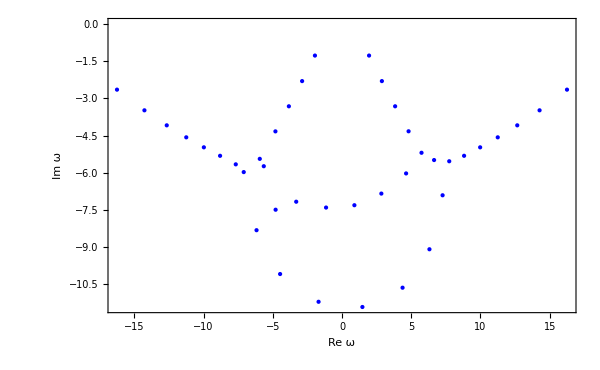

```mathematica
PlotFrequencies[modes]
```

This plot shows 41 points, because what GetModes does is calculate the eigenvalues of an N+1 by N+1 matrix, of which there are ofcourse 41. But not all are accurate, as the discretization of the equation isn't completely accurate. In practice, only the first few modes will be accurate, depending on the grid size and precision used.

Knowing this, we can just look at the first few modes:

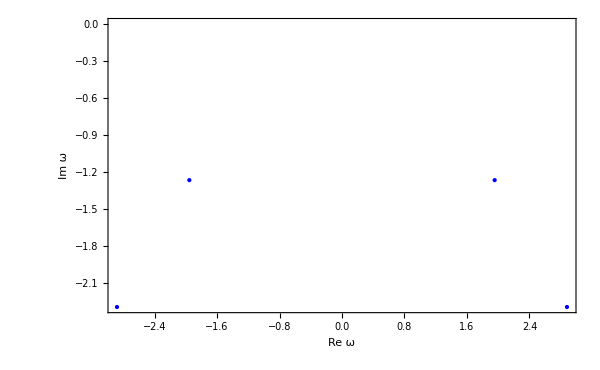
{-Graphics-,n | Re ω_n | Im ω_n
1 | ± 1.95433 | -1.26733
2 | ± 2.88026 | -2.29796
3 | ± 16.2485 | -2.64311
4 | ± 3.83664 | -3.3149}

```mathematica
ShowModes[modes,NModes->4]
```

Notice however that now only the first 4 modes shown are correct (in this case the modes lie almost on a straight line), even though from the previous plot we saw that the first 10 modes are roughly correct. They are sorted by imaginary part, and here inaccurate modes with higher imaginary part than the next accurate one occur, so this solution is not ideal.

## A more accurate solution

If we want more accurate modes, we can simply increase the gridsize and precision. Beware that for large grid sizes the precision may become the bottleneck. Ofcourse increasing either the gridsize or the precision will slow down the computation, but this should still take less than a minute:

{25.4743,Null}

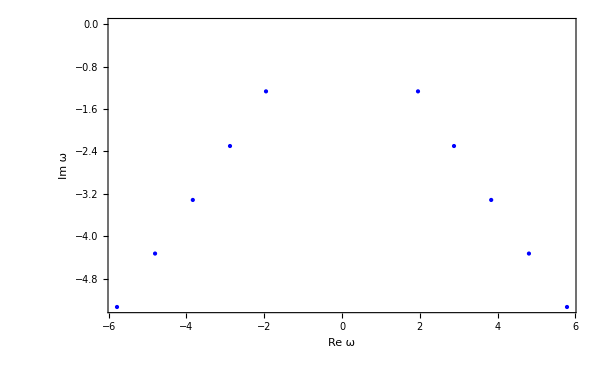
{-Graphics-,n | Re ω_n | Im ω_n
1 | ± 1.954330884 | -1.267327263
2 | ± 2.880262565 | -2.297957047
3 | ± 3.836632223 | -3.31490716
4 | ± 4.807392343 | -4.32587137
5 | ± 5.786181877 | -5.333622204
6 | ± 42.77346866 | -5.50954366
7 | ± 6.769957867 | -6.339430161
8 | ± 40.05666677 | -6.685780968
9 | ± 7.757068064 | -7.343966284
10 | ± 37.83035515 | -7.586859316}

```mathematica
modes2=GetModes[eqϕ/.q->1,{100}];//AbsoluteTiming
ShowModes[modes2,NModes->10]
```

Here we didn't specify the precision, so it defaults to half the grid size.

## Recommended use: GetAccurateModes

Since this large amount of incorrect modes is unavoidable using this method and the above solutions are tedious, there is a built in function to deal with this automatically:

GetAccurateModes[eq,{N,prec},{N2,prec2}] | computes modes with two gridsizes and precisions, returning only the common values

What this does is to compute the quasinormal mode spectrum using GetModes, with two sets of precision  {N,prec} and {N2,prec2}. Then it looks for modes in the first set which have a mode in the second set that is very close (with a difference less than 10^-Cutoff, where Cutoff is an option defaulting to 1). Of these modes it then returns only those digits that agree between both sets.

Provided the precision and gridsizes are not chosen too close together, and the background is either analytic or accurate enough not to be the source of errors, this practically (though not actually!) guarantees that the modes that are returned have converged.

It can be used as:

```mathematica
modesAccurate=GetAccurateModes[eqϕ/.q->1,{40,0},{100}];
```

Note that this computation is done almost instantaneously, as we had previously computed the modes with exactly these settings. By default GetModes remembers everything it computes, this can be turned off by setting $QNMMemory=False.

Since we automatically got rid of all the inaccurate modes, we can now simply display all of them:

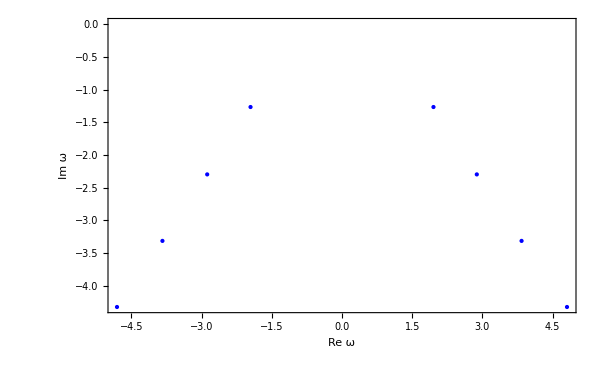
{-Graphics-,n | Re ω_n | Im ω_n
1 | ± 1.954330884 | -1.267327263
2 | ± 2.8802626 | -2.297957
3 | ± 3.83663 | -3.3149
4 | ± 4.81 | -4.3}

```mathematica
modesAccurate//ShowModes
```

This can be compared to the table for the scalar channel in appendix B of http://arxiv.org/abs/hep-th/0506184.

Accuracy is limited by the computation with 40 points at machine precision, increasing this we can easily get an accuracy comparable to the reference above:

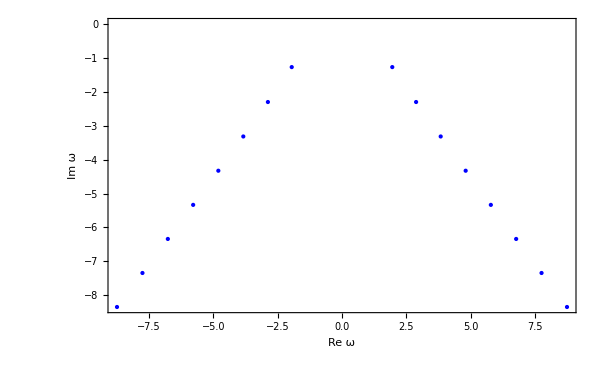
{-Graphics-,n | Re ω_n | Im ω_n
1 | ± 1.9543308837904205465964315600940940378303136499316 | -1.2673272634170641028504087400441669664023779300847
2 | ± 2.880262564849641861888009706 | -2.29795704651987325803990292
3 | ± 3.8366322229339033420617 | -3.31490716028999405305
4 | ± 4.80739234305317244 | -4.3258713695507753
5 | ± 5.7861818767378 | -5.333622203939
6 | ± 6.769957867 | -6.33943016
7 | ± 7.75707 | -7.344
8 | ± 8.75 | -8.3}

```mathematica
modesAccurate2=GetAccurateModes[eqϕ/.q->1,{60},{100}];
ShowModes[modesAccurate2,Precision->Infinity]
```

The option Precision → Infinity used above displays all the digits available in the result, showing nicely the decrease in accuracy with higher mode number.

More About

Related Tutorials

Overview

Extensions

Method

Related Wolfram Education Group Courses